```mathematica
pm = Import["C:\\Users\\Nikita\\Desktop\\TPM\\N_body_TPM\\Sources\\source-vs\\pm_m.txt","Table"];
```

```mathematica
PM={};
For[i=1 , i<Length[pm],i++,
AppendTo[PM, {pm[[i,1]], pm[[i,2]]}];
]
```

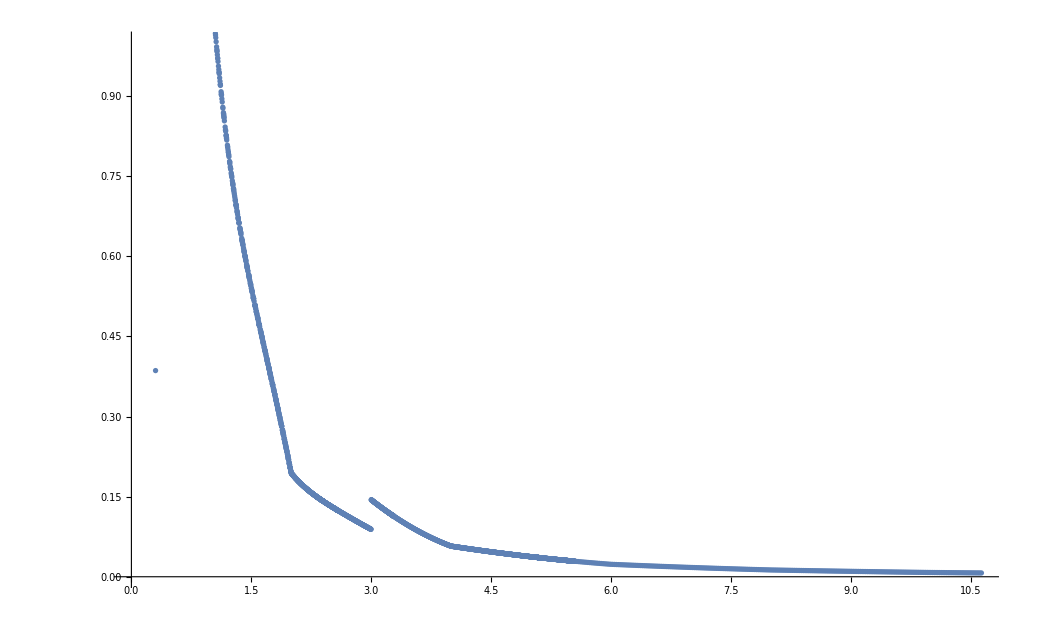

```mathematica
ListPlot[PM , PlotRange->1]
```

```mathematica
dir = Import["C:\\Users\\Nikita\\Desktop\\TPM\\N_body_TPM\\Sources\\source-vs\\dir_m.txt","Table"];
```

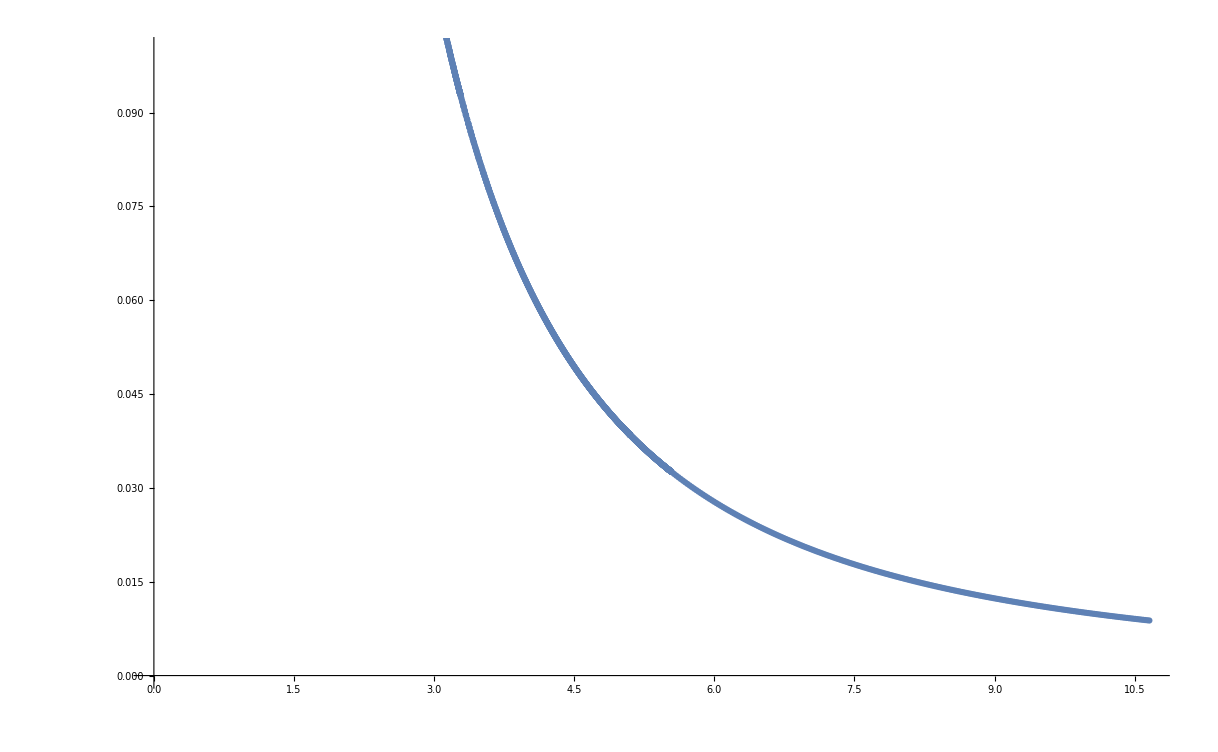

```mathematica
ListPlot[dir, PlotRange->0.1]
```

```mathematica
dif = {};
For[i=1 , i≤ Length[dir], i++,
AppendTo[dif, {dir[[i,1]], dir[[i, 2]]/ pm[[i,2]]}];
]
```

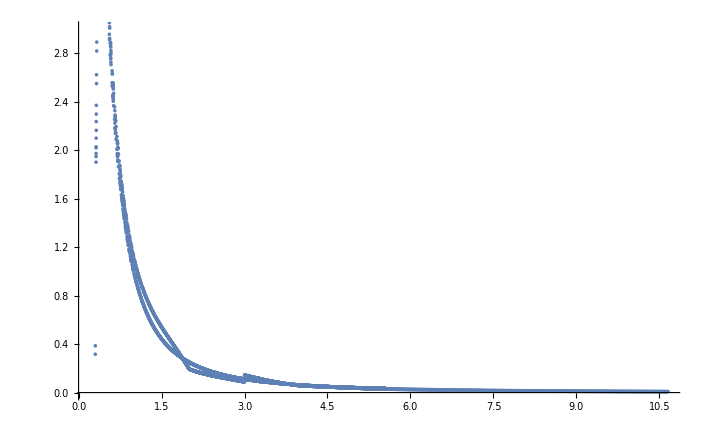

```mathematica
Show[%4, %8, PlotRange->{0,3}]
```

```mathematica
dif
```

{{5.1,1.07337},{5.09997,1.07337},{5.09992,1.07336},{5.09985,1.07336},{5.09974,1.07335},{5.09961,1.07334},{5.09946,1.07333},{5.09928,1.07332},{5.09907,1.07331},{5.09884,1.07329},{5.09859,1.07327},{5.0983,1.07325},{5.09799,1.07322},{5.09766,1.0732},{5.0973,1.07318},3138,{10.3526,1.24623},{10.3744,1.24602},{10.3962,1.24583},{10.418,1.24565},{10.4398,1.24549},{10.4616,1.24536},{10.4834,1.24523},{10.5052,1.24513},{10.527,1.24504},{10.5488,1.24496},{10.5705,1.24491},{10.5923,1.24487},{10.6141,1.24485},{10.6358,1.24485},{10.6576,1.24486}}
 |  |  |  |

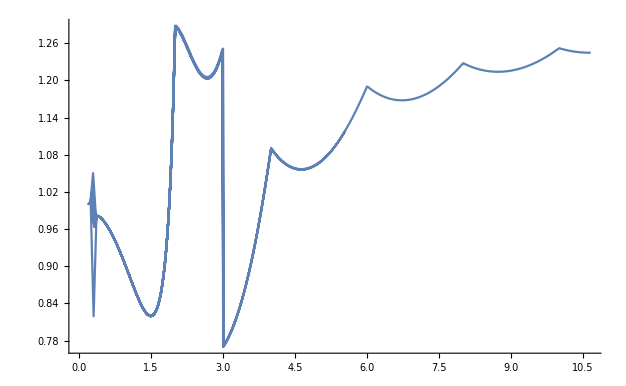

```mathematica
ListLinePlot[dif , PlotRange->All]
```

```mathematica
sh = Import["C:\\Users\\Nikita\\Desktop\\TPM\\N_body_TPM\\Sources\\source-vs\\sh_m.txt","Table"];
```

```mathematica
er={};
For[i=1 , i≤Length[sh], i++,
AppendTo[er, {sh[[i,2]], sh[[i,3]]}];
]
```

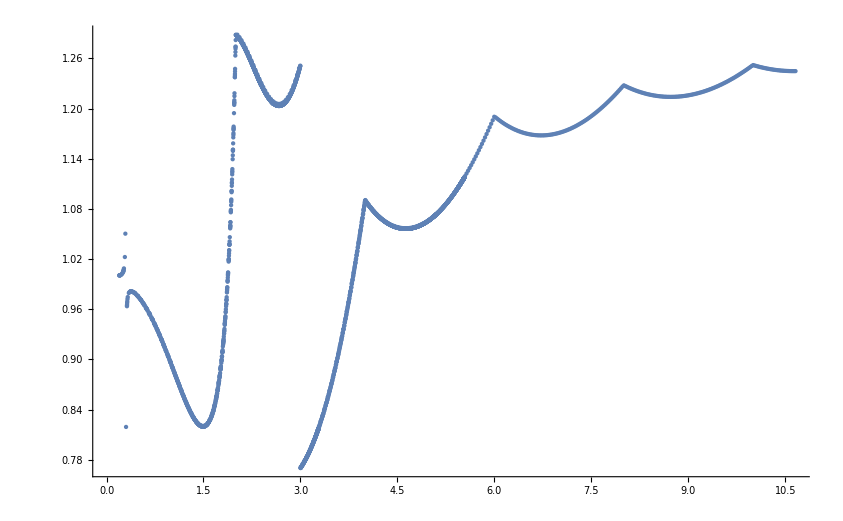

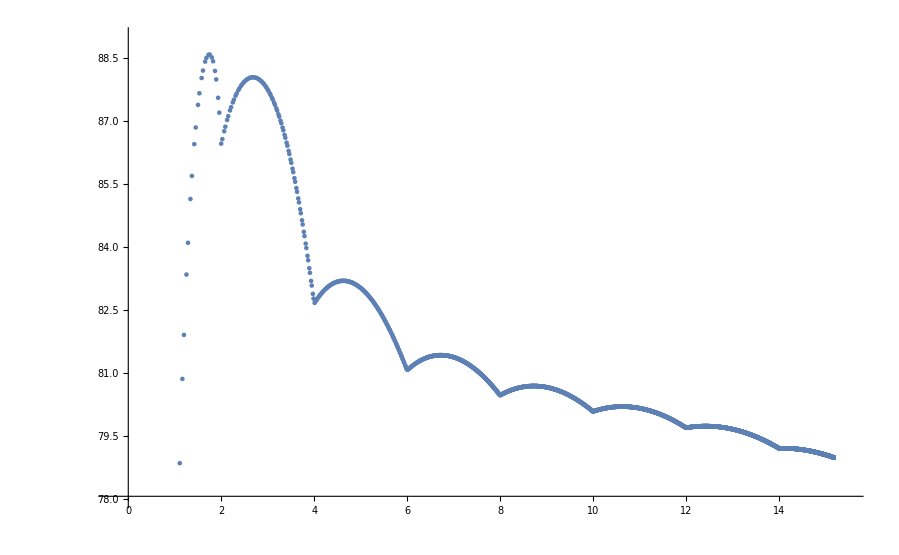

```mathematica
ListPlot[er]
```

```mathematica
er
```

{{5.1,1.07337},{5.09997,1.07337},{5.09992,1.07336},{5.09985,1.07336},{5.09974,1.07335},{5.09961,1.07334},{5.09946,1.07333},{5.09928,1.07332},{5.09907,1.0733},{5.09884,1.07329},{5.09859,1.07327},{5.0983,1.07325},{5.09799,1.07323},{5.09766,1.0732},{5.0973,1.07318},{5.09691,1.07315},{5.0965,1.07312},{5.09607,1.07309},{5.0956,1.07306},{5.09511,1.07302},{5.0946,1.07299},{5.09406,1.07295},{5.09349,1.07291},{5.0929,1.07287},3121,{10.1779,1.24856},{10.1997,1.24821},{10.2216,1.24787},{10.2434,1.24755},{10.2653,1.24725},{10.2871,1.24697},{10.309,1.24671},{10.3308,1.24646},{10.3526,1.24623},{10.3744,1.24602},{10.3962,1.24583},{10.418,1.24565},{10.4398,1.2455},{10.4616,1.24536},{10.4834,1.24523},{10.5052,1.24513},{10.527,1.24504},{10.5488,1.24497},{10.5705,1.24491},{10.5923,1.24487},{10.6141,1.24485},{10.6358,1.24485},{10.6576,1.24486}}
 |  |  |  |

```mathematica
sh
```

{{1,5.1,1.07337,0.00135712},{2,5.09997,1.07337,0.00271426},{3,5.09992,1.07336,0.00407143},{4,5.09985,1.07336,0.00542865},{5,5.09974,1.07335,0.00678593},{6,5.09961,1.07334,0.00814329},{7,5.09946,1.07333,0.00950075},{8,5.09928,1.07332,0.0108583},{9,5.09907,1.0733,0.012216},{10,5.09884,1.07329,0.0135739},{11,5.09859,1.07327,0.0149319},{12,5.0983,1.07325,0.01629},{13,5.09799,1.07323,0.0176484},{14,5.09766,1.0732,0.019007},3141,{3156,10.3962,1.24583,1.15103},{3157,10.418,1.24565,1.15075},{3158,10.4398,1.2455,1.15047},{3159,10.4616,1.24536,1.1502},{3160,10.4834,1.24523,1.14992},{3161,10.5052,1.24513,1.14964},{3162,10.527,1.24504,1.14937},{3163,10.5488,1.24497,1.14909},{3164,10.5705,1.24491,1.14882},{3165,10.5923,1.24487,1.14855},{3166,10.6141,1.24485,1.14828},{3167,10.6358,1.24485,1.14801},{3168,10.6576,1.24486,1.14774}}
 |  |  |  |

-Graphics-

```mathematica
f={};
For[i=1 , i≤Length[sh],i++,
AppendTo[f , {sh[[i,2]] , sh[[i,4]]}];
]
```